```mathematica
SetDirectory[NotebookDirectory[]];
w1=Import["1.dat"];
w2=Import["2.dat"];
w3=Import["3.dat"];
w4=Import["4.dat"];
w5=Import["5.dat"];
w6=Import["6.dat"];
w7=Import["7.dat"];
```

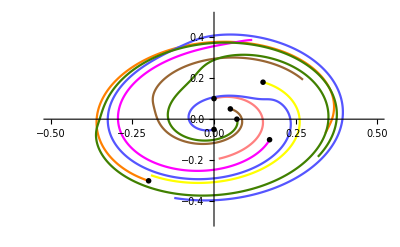

```mathematica
Show[ListLinePlot[{w1},PlotStyle->Directive[Orange]],ListLinePlot[w2,PlotStyle->Directive[Magenta]],ListLinePlot[w3,PlotStyle->Directive[Yellow]],ListLinePlot[w4,PlotStyle->Directive[Pink]] ,ListLinePlot[w5,PlotStyle->Directive[Brown]] ,ListLinePlot[w6,PlotStyle->Directive[Lighter@Blue]] ,ListLinePlot[w7,PlotStyle->Directive[Hue[5/4,4/2,1/2]]]  ,Graphics[{PointSize[0.01],Point[{0.17,-0.1}], Point[{ -0.2,-0.3}], Point[{ 0.,0.1}],Point[{ 0.15,0.18}],Point[{ 0.07,0.}],Point[{0.05,0.05}],Point[{ 0.,-0.05}]}], PlotRange->{{-.5,.5},{-.5,.5}},BaseStyle->Red]
```

```mathematica
{xs,ys}=NDSolveValue[{x'[t]==(0.4+0.3*Sin[0.5*t])*y[t]+0.1*x[t]-x[t]^3-x[t]*y[t]^2,y'[t]==-(0.4+0.3*Sin[0.5*t])*x[t]+0.2*y[t]-y[t]^3-y[t]*x[t]^2,x[0]==y[0]==-0.1},{x,y},{t,50}]
```

{InterpolatingFunction[{{0., 50.}}, <>],InterpolatingFunction[{{0., 50.}}, <>]}

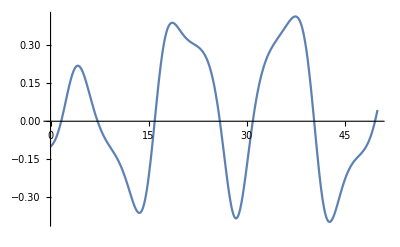

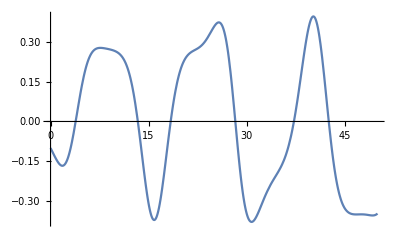

```mathematica
Plot[ys[t],{t,0,50}]
Plot[xs[t],{t,0,50}]
```

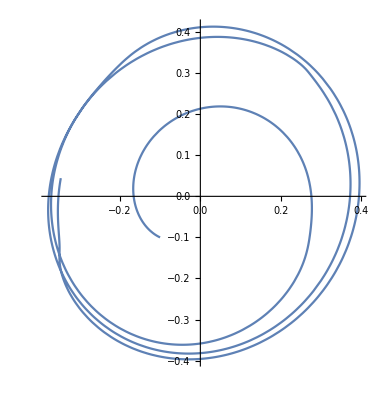

```mathematica
ParametricPlot[{xs[t],ys[t]},{t,0,50}]
```